### Zero VZ

The 2 in front comes from the two (± vF k) branches of the dispersion. L = N a0

```mathematica
Integrate[2(U a0)/(2π vF)1/(√(Δ^2+ϵ^2)),{ϵ,-ϵ0,ϵ0}, Assumptions->{ϵ0>0,Δ>0}]
Normal[Simplify[Series[%,{Δ,0,1}],ϵ0>0]]
Simplify[Solve[%==1,Δ],{U>0,L>0,vF>0, a0>0}]
```

(a0 U Log[1+(2 ϵ0 (ϵ0+√(Δ^2+ϵ0^2)))/Δ^2])/(π vF)

(a0 U Log[(4 ϵ0^2)/Δ^2])/(π vF)

{{Δ→-2 ⅇ^(-(π vF)/(2 a0 U)) ϵ0},{Δ→2 ⅇ^(-(π vF)/(2 a0 U)) ϵ0}}

#### A more exact dispersion cannot be integrated

```mathematica
Integrate[2(U a0^2)/(2π L)1/(√(Δ^2+(2t Cos[ka]-μ)^2)),{ka,-π,π}, Assumptions->{μ>0,t>0}]
```

$Aborted

### Finite VZ

#### Changing variables from vk to Ek

```mathematica
Simplify[1/D[√(Δ^2+vk^2),vk]/.vk->√(Ek^2-Δ^2),Ek>0]
```

Ek/(√(Ek^2-Δ^2))

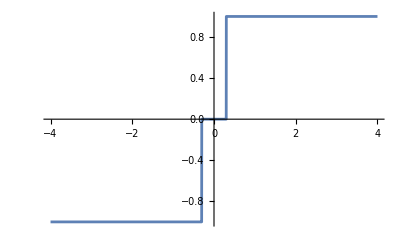

```mathematica
tanh0[x_] = 2UnitStep[x]-1;
Plot[(tanh0[Vz+Ek]-tanh0[Vz-Ek])/2/.Vz->0.3,{Ek,-4,4}]
```

The integrand is 2(U a0^2)/(2π vF L)Ek/(√(Ek^2-Δ^2))1/Ek(tanh0[Vz+Ek]-tanh0[Vz-Ek])/2
The integral extends from Emin = max(Δ,|VZ|) to ~ϵ0
The extra factor 2 comes from the two solutions of ϵ for each Ek

```mathematica
Integrate[4(U a0^2)/(2π vF L)1/(√(Ek^2-Δ^2)),{Ek,Emin,ϵ0}, Assumptions->{ϵ0>Emin>Δ>0}]
```

(a0^2 U Log[((-Emin+√(Emin^2-Δ^2)) (ϵ0+√(-Δ^2+ϵ0^2)))/((Emin+√(Emin^2-Δ^2)) (-ϵ0+√(-Δ^2+ϵ0^2)))])/(L π vF)

```mathematica
FullSimplify[Series[((-Emin+√(Emin^2-Δ^2)) (ϵ0+√(-Δ^2+ϵ0^2)))/((Emin+√(Emin^2-Δ^2)) (-ϵ0+√(-Δ^2+ϵ0^2)))/.{ϵ0->√(Δ^2+ϵ0^2/λ^2)},{λ,0,-1}],{ϵ0>0,Emin>0, λ>0}]//Normal
FullSimplify[(a0^2 U)/(L π vF)(Log[%])/.{Emin->VZ,λ->1}]
```

-(4 (Δ^2+2 Emin (-Emin+√((Emin-Δ) (Emin+Δ)))) ϵ0^2)/(Δ^4 λ^2)

(a0^2 U Log[-(4 (Δ^2+2 VZ (-VZ+√(VZ^2-Δ^2))) ϵ0^2)/Δ^4])/(L π vF)

```mathematica
(a0^2 U Log[-(4 (Δ^2+2 VZ (-VZ+√(VZ^2-Δ^2))) ϵ0^2)/Δ^4])/(L π vF)/.VZ->Δ
```

(a0^2 U Log[(4 ϵ0^2)/Δ^2])/(L π vF)

```mathematica
Solve[(a0^2 U Log[-(4 (Δ^2+2 VZ (-VZ+√(VZ^2-Δ^2))) ϵ0^2)/Δ^4])/(L π vF)==1,Δ]
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{Δ→-2 √(-ⅇ^(-(L π vF)/(2 a0^2 U)) VZ ϵ0-ⅇ^(-(L π vF)/(a0^2 U)) ϵ0^2)},{Δ→2 √(-ⅇ^(-(L π vF)/(2 a0^2 U)) VZ ϵ0-ⅇ^(-(L π vF)/(a0^2 U)) ϵ0^2)},{Δ→-2 √(ⅇ^(-(L π vF)/(2 a0^2 U)) VZ ϵ0-ⅇ^(-(L π vF)/(a0^2 U)) ϵ0^2)},{Δ→2 √(ⅇ^(-(L π vF)/(2 a0^2 U)) VZ ϵ0-ⅇ^(-(L π vF)/(a0^2 U)) ϵ0^2)}}

```mathematica
Simplify[(2 √(ⅇ^(-(L π vF)/(2 a0^2 U)) VZ ϵ0-ⅇ^(-(L π vF)/(a0^2 U)) ϵ0^2))/(2ϵ0)/.{ⅇ^(-(L π vF)/(2 a0^2 U))->Δ0/(2ϵ0),ⅇ^(-(L π vF)/(a0^2 U))->(Δ0/(2ϵ0))^2}]
```

(√((2 VZ-Δ0) Δ0))/(2 ϵ0)